Ejercicio 2

Calcula las integrales de las siguientes funciones en los conjuntos que se indican.
a) f(x,y)=x y en el conjunto A limitado por la recta y-x+1=0 y la parábola y^2-2x-6=0.
b) f(x,y)= x en el conjunto A limitado por las curvas y=x^4, y=3x-x^2.
c) f(x,y)= x √(y^2-x^2) en el triángulo de vértices (0,0), (0,1),(1,1).
d) f(x,y)= y^2-x en el conjunto A limitado por las curvas x-y^2=0,  x+2 y^2-3=0.
e) f(x,y)=√(4 x^2-y^2) en el conjunto A limitado por las rectas x=1, y=0, y=x.
f) f(x,y,z)=1/(1+x+y+z)^3 en el conjunto A={(x,y,z)∈ℝ^3:x≥0, y≥0, z≥0, x+y+z≤1}.
g) f(x,y,z)=z  en el conjunto A={(x,y,z)∈ℝ^3: z≥0, x^2+y^2/4+z^2/9≤1}.

```mathematica
(* a) *)
```

```mathematica
lim1=x-1;
lim2p=√(2x+6);
lim2n=-√(2x+6);
```

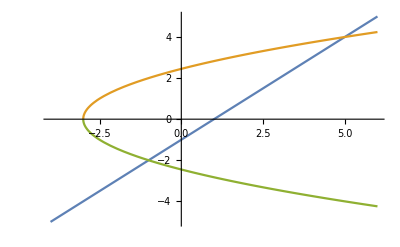

```mathematica
Plot[{lim1,lim2p,lim2n},{x,-4,6}]
```

```mathematica
(* vía 1 *)
```

```mathematica
reg=ImplicitRegion[y^2-2x-6<0&&y>x-1,{x,y}]
```

ImplicitRegion[-6-2 x+y^2<0&&y>-1+x,{x,y}]

```mathematica
RegionPlot[reg]
```

-Graphics-

```mathematica
Integrate[x y,{x,y}∈reg]
```

36

```mathematica
(* via 2 *)
```

```mathematica
(*conviene integrar x primero *)
```

```mathematica
Solve[y^2-2x-6==0,x]
```

{{x→1/2 (-6+y^2)}}

```mathematica
Solve[y^2-2x-6==0/.x-> y+1,y]
```

{{y→-2},{y→4}}

```mathematica
Integrate[x y,{y,-2.,4},{x,1/2 (-6+y^2),y+1}]
```

36.

```mathematica
check=Integrate[1,{x,-3,5},{y,0,lim2p}]-Integrate[1,{x,1,5.},{y,0,lim1}]+Integrate[1,{x,-3,-1},{y,lim2n,0}]+Integrate[1,{x,-1,1},{y,lim1,0}]
```

18.

```mathematica
(*
b) f(x,y)= xen el conjunto A limitado por las curvas y=x^4, y=3x-x^2.
*)
```

```mathematica
lim1=x^4;
lim2=3x-x^2;
```

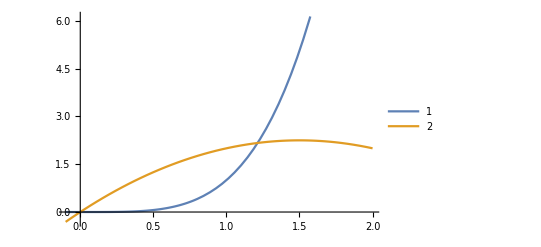

```mathematica
Plot[{lim1,lim2},{x,-0.1,2},PlotLegends->Automatic]
```

```mathematica
reg=ImplicitRegion[y-x^4>0&&y<3x-x^2,{x,y}]
```

ImplicitRegion[-x^4+y>0&&y<3 x-x^2,{x,y}]

```mathematica
RegionPlot[reg]
```

-Graphics-

```mathematica
NIntegrate[x ,{x,y}∈reg]
```

0.712639

```mathematica
NSolve[{x^4==3x-x^2,x>0},x]
```

{{x→1.21341}}

```mathematica
NIntegrate[x ,{x,0,1.2134116627622296},{y,lim1,lim2}]
```

0.712639

```mathematica
(*
c) f(x,y)= x √(y^2-x^2)en el triángulo de vértices(0,0), (0,1),(1,1).
*)
```

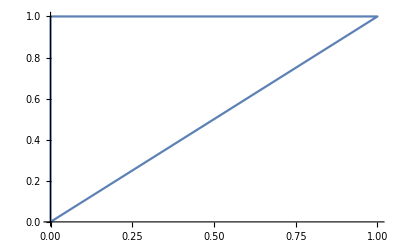

```mathematica
ListPlot[{{0,0},{0,1},{1,1},{0,0}},Joined->True]
```

```mathematica
reg=Triangle[{{0,0},{0,1},{1,1}}]
```

Triangle[{{0,0},{0,1},{1,1}}]

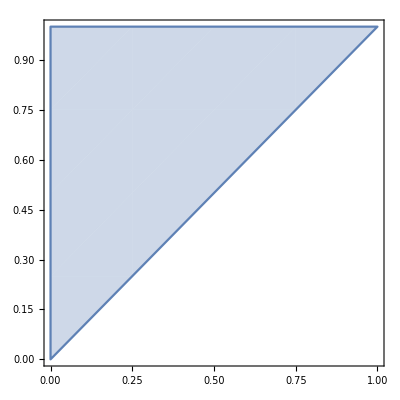

```mathematica
RegionPlot[reg]
```

```mathematica
NIntegrate[x √(y^2-x^2),{x,y}∈reg]
```

0.0833333

```mathematica
NIntegrate[x √(y^2-x^2),{y,0,1},{x,0,y}]
```

0.0833333

```mathematica
(*
d) f(x,y)= y^2-x en el conjunto A limitado por las curvas x-y^2=0,  x+2 y^2-3=0.
*)
```

```mathematica
Solve[x+2y^2-3==0,y]
```

{{y→-(√(3-x))/(√2)},{y→(√(3-x))/(√2)}}

```mathematica
Solve[x-y^2==0,y]
```

{{y→-√x},{y→√x}}

```mathematica
lim1p=Sqrt[x];
lim1n=-Sqrt[x];
lim2p=Sqrt[(-x+3)/2];
lim2n=-Sqrt[(-x+3)/2];
```

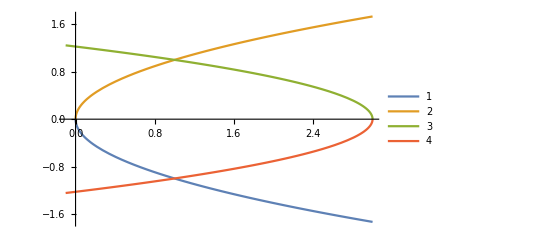

```mathematica
Plot[{lim1n,lim1p,lim2p,lim2n},{x,-0.1,3},PlotLegends->Automatic]
```

```mathematica
reg=ImplicitRegion[ x+2 y^2-3<0&&x-y^2>0,{x,y}]
```

ImplicitRegion[-3+x+2 y^2<0&&x-y^2>0,{x,y}]

```mathematica
RegionPlot[reg]
```

-Graphics-

```mathematica
NIntegrate[ y^2-x,{x,y}∈reg]
```

-4.8

```mathematica
NIntegrate[ y^2-x,{x,0,1},{y,lim1n,lim1p}]+NIntegrate[ y^2-x,{x,1,3},{y,lim2n,lim2p}]
```

-4.8

```mathematica
(*
e) f(x,y)=√(4 x^2-y^2)en el conjunto A limitado por las rectas x=1, y=0, y=x.
*)
```

```mathematica
lim1=0;
lim2=x;
```

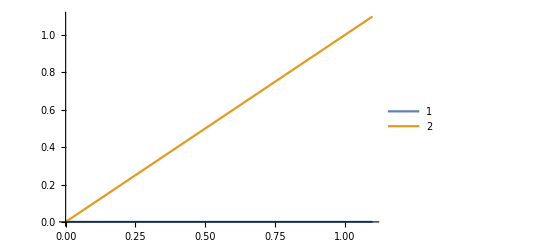

```mathematica
Plot[{lim1,lim2},{x,0,1.1},PlotLegends->Automatic]
```

```mathematica
reg=Triangle[{{0,0},{1,0},{1,1}}]
```

Triangle[{{0,0},{1,0},{1,1}}]

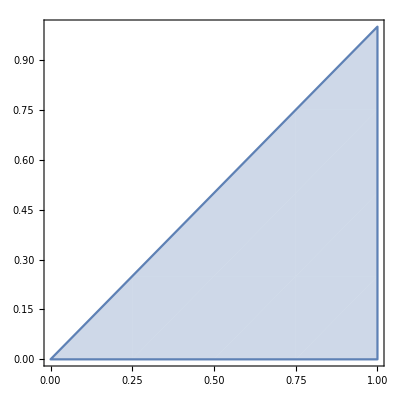

```mathematica
RegionPlot[reg]
```

```mathematica
NIntegrate[√(4 x^2-y^2),{x,y}∈reg]
```

0.637762

```mathematica
NIntegrate[√(4 x^2-y^2),{x,0,1},{y,0,lim2}]
```

0.637741

```mathematica
(*
f) f(x,y,z)=1/(1+x+y+z)^3 en el conjunto A={(x,y,z)∈ℝ^3:x≥0, y≥0, z≥0, x+y+z≤1}.
*)
```

```mathematica
Plot3D[{-x-y+1,x==0,y==0},{x,0,0.6},{y,0,0.6}]
```

-Graphics3D-

```mathematica
reg=ImplicitRegion[x≥0&& y≥0&& z≥0&& x+y+z≤1,{x,y,z}]
```

ImplicitRegion[x≥0&&y≥0&&z≥0&&x+y+z≤1,{x,y,z}]

```mathematica
RegionPlot3D[reg]
```

-Graphics3D-

```mathematica
NIntegrate[1/(1+x+y+z)^3,{x,y,z}∈reg]
```

0.0340736

```mathematica
NIntegrate[1/(1+x+y+z)^3,{x,0,1},{y,0,1-x},{z,0,1-x-y}]
```

0.0340736

```mathematica
(*
g) f(x,y,z)=z en el conjunto A={(x,y,z)∈ℝ^3: z≥0, x^2+y^2/4+z^2/9≤1}.
*)
```

```mathematica
reg=ImplicitRegion[z≥0&& x^2+y^2/4+z^2/9≤1,{x,y,z}]
```

ImplicitRegion[z≥0&&x^2+y^2/4+z^2/9≤1,{x,y,z}]

```mathematica
RegionPlot3D[reg]
```

-Graphics3D-

```mathematica
NIntegrate[z,{x,y,z}∈reg]
```

14.1372

```mathematica
NIntegrate[z,{x,0,1},{y,0,1-x},{z,0,1-x-y}]
```

```mathematica
Reduce[x^2+y^2/4+z^2/9≤1,z]//Simplify
```

-2≤y≤2&&((z==0&&(2 x+√(4-y^2)==0||√(4-y^2)==2 x))||(-3/2 √(4-4 x^2-y^2)≤z≤3/2 √(4-4 x^2-y^2)&&2 x+√(4-y^2)>0&&√(4-y^2)>2 x))

```mathematica
NIntegrate[z,{y,-2,2},{x,-√(4-y^2)/2,√(4-y^2)/2},{z,0,3/2 √(4-4 x^2-y^2)}]
```

14.1372